```mathematica
fi0[x_] := 1
fi1[x_] := E^x
fi2[x_] := E^(2*x)
fi3[x_] := E^(3*x)
fi4[x_] := E^(4*x)
```

```mathematica
fi[x_] := a0*fi0[x] + a1*fi1[x] + a2*fi2[x]+a3*fi3[x]+a4*fi4[x]
```

```mathematica
system:= {
fi[1]== 1,
fi[2]==12,
fi[3]==134,
fi[4]==1045,
fi[5]== 10112
}
NSolve[system, {a0, a1, a2, a3, a4}]
```

{{a0→3.85687,a1→-2.35437,a2→0.486656,a3→-0.00268485,a4→0.0000175509}}

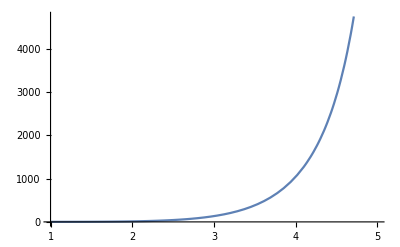

```mathematica
FI[x_] := 3.8568735215657357*fi0[x] + -2.354366204933286*fi1[x] + 0.4866556240483907*fi2[x]+-0.00268484737828783*fi3[x]+0.0000175508700918904*fi4[x] // Simplify
Plot[FI[x], {x, 1, 5}]
```

```mathematica
ksi0[x_] := 1
ksi1[x_]:=Sin[x]
ksi2[x_]:=Cos[x]
ksi3[x_]:=Sin[2*x]
ksi4[x_]:=Cos[2*x]
```

```mathematica
m[x_] := a0*ksi0[x]+a1*ksi1[x]+a2*ksi2[x]+a3*ksi3[x]+a4*ksi4[x]
```

```mathematica
mSys := {
m[0]==-1,
m[Pi/2]==0,
m[Pi]==1,
m[3Pi/2]==0,
m[2Pi-0.001]==-1
}
```

```mathematica
mSol := NSolve[mSys, {a0, a1, a2, a3, a4}]
```

```mathematica
M[x_] := m[x] /.mSol[[1]]
```

```mathematica
n[x_]:= b0*ksi0[x]+b1*ksi1[x]+b2*ksi2[x]+b3*ksi3[x]+b4*ksi4[x]
```

```mathematica
nSys := {
n[0]==-1,
n[Pi/2]==-2,
n[Pi]==-1,
n[3Pi/2]==-2,
n[2Pi-0.001]==-1
}
```

```mathematica
nSol:=NSolve[nSys,{b0,b1,b2,b3,b4}]
```

```mathematica
nSol
```

{{b0→-1.5,b1→0.,b2→0.,b3→-0.0005,b4→0.5}}

```mathematica
KSI[x_]:=a0 + a1*Cos[x]+b1*Sin[x]+a2*Cos[2*x]+b2*Sin[2*x]+a3*Cos[3*x]+b3*Sin[3*x]+a4*Cos[4*x]+b4*Sin[4*x] /.mSol[[1]] /.nSol[[1]]
```

```mathematica
KSI[x]
```

0.-1. Cos[2 x]+0.00025 Cos[3 x]-0.0005 Sin[3 x]+0.5 Sin[4 x]

```mathematica
KSI[Pi/2]
```

1.0005